```mathematica
SetDirectory[NotebookDirectory[]];
```

## Some magnetic field configurations - flat spacetime

In this part we will use some formulas for magnetic field, from Jackson - Classical electrodynamics. 
We use magnetic flux auction Ψ(r,θ) and ϕ component of covariant electromagnetic four-vector potential is given by: Ψ(r,θ) = A_ϕ(r,θ)
-Graphics--Graphics-

```mathematica
Clear[Phi];r^2 D[D[Phi[r,θ],r],r]+D[D[Phi[r,θ],θ],θ]-Cot[θ]D[Phi[r,θ],θ];
Br=Simplify[D[Phi[r,θ],θ]/(r^2 Sin[θ])];Bθ=Simplify[-D[Phi[r,θ],r]/(r Sin[θ])];
```

Function fceCON[text_] will just show the magnetic filed lines using Ψ(r,θ) = const. condition

```mathematica
fceOKNO[x1_,x2_,z1_,z2_,text_]:=Quiet[Show[{StreamPlot[fieldXZ,{x,x1,x2},{z,z1,z2},BaseStyle->{15,Background->White},FrameLabel->{x,z},ImageSize->300,PlotRange->{{x1,x2},{z1,z2}},RotateLabel->False,Epilog->{Text[text,Scaled[{0.5,0.9}]]}],
ContourPlot[ Abs[Phi[√(x^2+z^2),ArcTan[x/z]]],{x,-12,12},{z,-12,12},ContourShading->None,ContourStyle->Thickness[0.005]]}]];
fceCON[text_]:=GraphicsColumn[{fceOKNO[0,10,0,10,text],fceOKNO[-11,11,-11,11,text]},Spacings->0]
```

### Uniform

```mathematica
Clear[B];Phi[r_,θ_]:=B/2 r^2 Sin[θ]^2;
Simplify[r^2 D[D[Phi[r,θ],r],r]+D[D[Phi[r,θ],θ],θ]-Cot[θ]D[Phi[r,θ],θ]]

Br=Simplify[D[Phi[r,θ],θ]/(r^2 Sin[θ])];Bθ=Simplify[-D[Phi[r,θ],r]/(r Sin[θ])];Print["{Br,Bθ}=",{Br,Bθ}]
field=Simplify[TransformedField["Spherical"-> "Cartesian",{Br,Bθ,0},{r,θ,ϕ}->{x,y,z}]/.y->0];
fieldXZ={field[[1]],field[[3]]};Print["{Bx,Bz}=",fieldXZ]
```

0

{Br,Bθ}={B Cos[θ],-B Sin[θ]}

{Bx,Bz}={0,B}

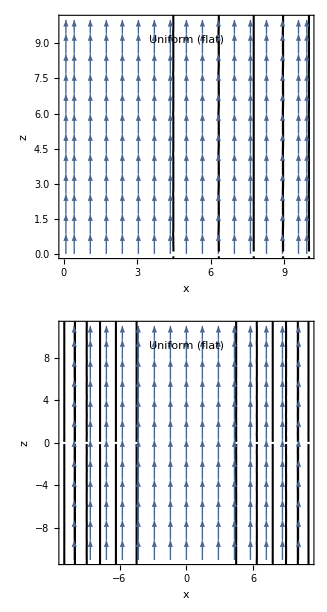

```mathematica
B=1;p1=fceCON["Uniform (flat)"]
```

### Monopole

```mathematica
Clear[e];Phi[r_,θ_]:=e  Cos[θ];
Simplify[r^2 D[D[Phi[r,θ],r],r]+D[D[Phi[r,θ],θ],θ]-Cot[θ]D[Phi[r,θ],θ]]

Br=Simplify[D[Phi[r,θ],θ]/(r^2 Sin[θ])];Bθ=Simplify[-D[Phi[r,θ],r]/(r Sin[θ])];Print["{Br,Bθ}=",{Br,Bθ}]
field=Simplify[TransformedField["Spherical"-> "Cartesian",{Br,Bθ,0},{r,θ,ϕ}->{x,y,z}]/.y->0];
fieldXZ={field[[1]],field[[3]]};Print["{Bx,Bz}=",fieldXZ]
```

0

{Br,Bθ}={-e/r^2,0}

{Bx,Bz}={-(e x)/((x^2+z^2)^(3/2)),-(e z)/((x^2+z^2)^(3/2))}

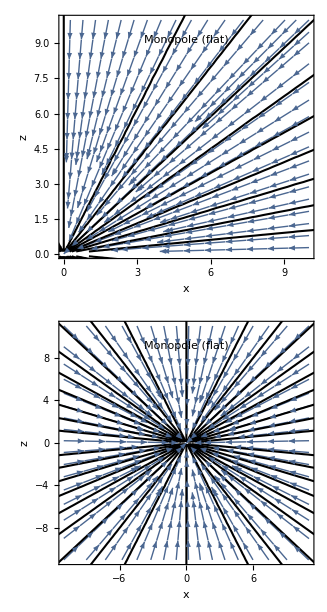

```mathematica
e=1;p2=fceCON["Monopole (flat)"]
```

### Dipole

```mathematica
Clear[k];Phi[r_,θ_]:=k(r^2 Sin[θ]^2)/r^3;
Simplify[r^2 D[D[Phi[r,θ],r],r]+D[D[Phi[r,θ],θ],θ]-Cot[θ]D[Phi[r,θ],θ]]

Br=Simplify[D[Phi[r,θ],θ]/(r^2 Sin[θ])];Bθ=Simplify[-D[Phi[r,θ],r]/(r Sin[θ])];Print["{Br,Bθ}=",{Br,Bθ}]
field=Simplify[TransformedField["Spherical"-> "Cartesian",{Br,Bθ,0},{r,θ,ϕ}->{x,y,z}]/.y->0];
fieldXZ={field[[1]],field[[3]]};Print["{Bx,Bz}=",fieldXZ]
```

0

{Br,Bθ}={(2 k Cos[θ])/r^3,(k Sin[θ])/r^3}

{Bx,Bz}={(3 k x z)/((x^2+z^2)^(5/2)),-(k (x^2-2 z^2))/((x^2+z^2)^(5/2))}

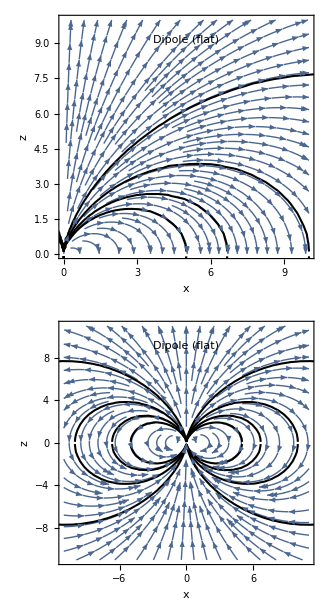

```mathematica
k=1;p3=fceCON["Dipole (flat)"]
```

### Loop

```mathematica
Clear[a];
fceK2[r_,θ_,a_]:=(4 a r Sin[θ])/(a^2+r^2+2a r Sin[θ]);
Phi[r_,θ_]:=1/(4π)(4 a r Sin[θ])/(√(a^2+r^2+2a r Sin[θ]))(((2-fceK2[r,θ,a])EllipticK[fceK2[r,θ,a]]-2EllipticE[fceK2[r,θ,a]])/fceK2[r,θ,a]);

Simplify[r^2 D[D[Phi[r,θ],r],r]+D[D[Phi[r,θ],θ],θ]-Cot[θ]D[Phi[r,θ],θ]]

Br=Simplify[D[Phi[r,θ],θ]/(r^2 Sin[θ])];Bθ=Simplify[-D[Phi[r,θ],r]/(r Sin[θ])];Print["{Br,Bθ}=",{Br,Bθ}]
field=Simplify[TransformedField["Spherical"-> "Cartesian",{Br,Bθ,0},{r,θ,ϕ}->{x,y,z}]/.y->0];
fieldXZ={field[[1]],field[[3]]};
```

0

{Br,Bθ}={(a^2 Cos[θ] EllipticE[(4 a r Sin[θ])/(a^2+r^2+2 a r Sin[θ])])/(π (a^2+r^2-2 a r Sin[θ]) √(a^2+r^2+2 a r Sin[θ])),(Csc[θ] ((r^2+a^2 Cos[2 θ]) EllipticE[(4 a r Sin[θ])/(a^2+r^2+2 a r Sin[θ])]-EllipticK[(4 a r Sin[θ])/(a^2+r^2+2 a r Sin[θ])] (a^2+r^2-2 a r Sin[θ])))/(2 π (a^2+r^2-2 a r Sin[θ]) √(a^2+r^2+2 a r Sin[θ]))}

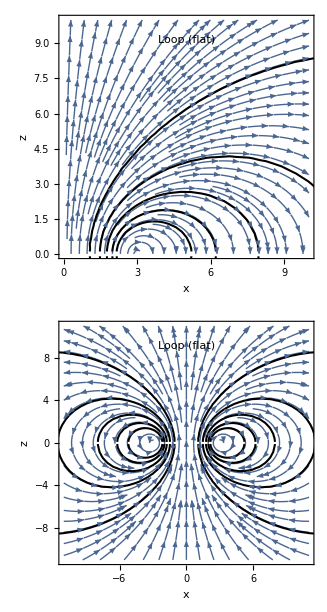

```mathematica
a=3;p4=fceCON["Loop (flat)"]
```

### Show

```mathematica
picFLAT=GraphicsRow[{p1,p2,p3,p4},Spacings->-30]
```

-Graphics-

```mathematica
Export["picFLAT.jpg",picFLAT];
```

## some configurations of magnetic field in Schwarzschild BH spacetime

```mathematica
fceCONBH[text_]:=
ContourPlot[ Abs[Phi[√(x^2+z^2),ArcTan[x/z]]],{x,0,12},{z,0,12},ContourShading->None,Contours->20,ContourStyle->{Thickness[0.005]},BaseStyle->{15,Background->White},FrameLabel->{x,z},ImageSize->300,RotateLabel->False,WorkingPrecision->77,Epilog->{Text[text,Scaled[{0.5,0.9}]],LightGray,Disk[{0,0},2M]}];
```

### Uniform magnetic field

```mathematica
Clear[B,M];Phi[r_,θ_]:=B/2 r^2 Sin[θ]^2;
Simplify[1/Sin[θ](D[(1-(2M)/r)D[Phi[r,θ],r],r])+1/r^2 D[1/Sin[θ] D[Phi[r,θ],θ],θ]]
```

0

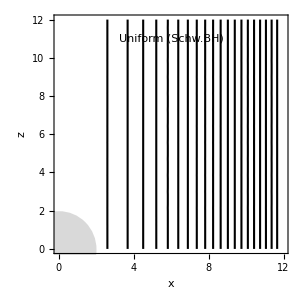

```mathematica
B=1;M=1;p1=fceCONBH["Uniform (Schw.BH)"]
```

### Monopole

```mathematica
Clear[e,M];Phi[r_,θ_]:=e  Cos[θ];
Simplify[1/Sin[θ](D[(1-(2M)/r)D[Phi[r,θ],r],r])+1/r^2 D[1/Sin[θ] D[Phi[r,θ],θ],θ]]
```

0

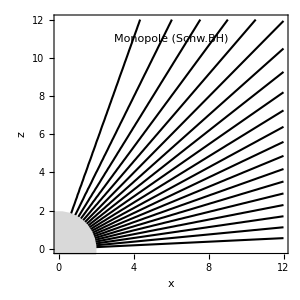

```mathematica
e=1;M=1;p2=fceCONBH["Monopole (Schw.BH)"]
```

### Dipole

```mathematica
Clear[M];Limit[(Log[1-(2M)/r]+(2M)/r(1+M/r)),M->0]
```

0

```mathematica
Clear[k,M];Phi[r_,θ_]:=k r^2 Sin[θ]^2(Log[1-(2M)/r]+(2M)/r(1+M/r));
Simplify[1/Sin[θ](D[(1-(2M)/r)D[Phi[r,θ],r],r])+1/r^2 D[1/Sin[θ] D[Phi[r,θ],θ],θ]]
```

0

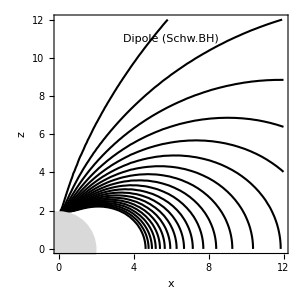

```mathematica
k=1;M=1;p3=fceCONBH["Dipole (Schw.BH)"]
```

### Petterson loop

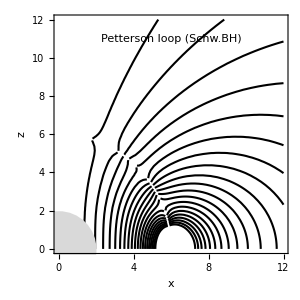

```mathematica
Clear[ii,M,a,alpha,Vl,Ul,RRin,RRout,AϕsumPoutX,AϕsumPinX,Phi];
alpha[l_]:= (-1)^((l+2)/2)(4 √π(l+3/2) Gamma[1/2(l+1)])/(a/(a-2 M)(l+2)Factorial[(l/2)] √(1-(2M)/a));Ul[l_,u_]:=u^2(2M)^(l+2)JacobiP[l,2,0,(1-2u)];Vl[l_,u_]:=(-Ul[l,r/(2M)]Integrate[Simplify[(r/(2M))/((1-r/(2M))Ul[l,r/(2M)]^2)],r]/.r->2M u);
RRin[l_,r_]:=r^2(2M)^l JacobiP[l,2,0,(1-r/M)]Vl[l,a/(2M)];
RRout[l_,r_]:=a^2(2M)^l JacobiP[l,2,0,(1-a/M)]Vl[l,r/(2M)];

ii=7;
AϕsumPoutX[r_,θ_,a_]=Sum[alpha[l]RRout[l,r] Sin[θ]^2 GegenbauerC[l,3/2,Cos[θ]],{l,0,2ii,2}];
AϕsumPinX[r_,θ_,a_]=Sum[alpha[l]RRin[l,r] Sin[θ]^2 GegenbauerC[l,3/2,Cos[θ]],{l,0,2ii,2}];
AϕsumPX[r_,θ_,a_]=If[r<=a,AϕsumPinX[r,θ,a],AϕsumPoutX[r,θ,a]];

a=6;M=1;Phi[r_,θ_]=AϕsumPX[r,θ,a];
p4=fceCONBH["Petterson loop (Schw.BH)"]
```

### parabolic

```mathematica
Clear[k,M,r0];
Phi[r_,θ_]:=k((r-2M)(1-Cos[θ])-r0 Cos[θ]-2M(1+Cos[θ])Log[1+Cos[θ]]);

Simplify[1/Sin[θ](D[(1-(2M)/r)D[Phi[r,θ],r],r])+1/r^2 D[1/Sin[θ] D[Phi[r,θ],θ],θ]]
```

0

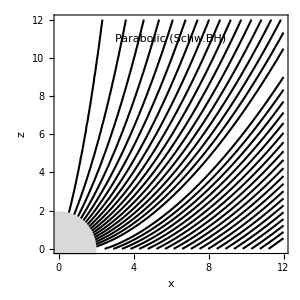

```mathematica
M=1;r0=5.4;k=1;p5=fceCONBH["Parabolic (Schw.BH)"]
```

### Show

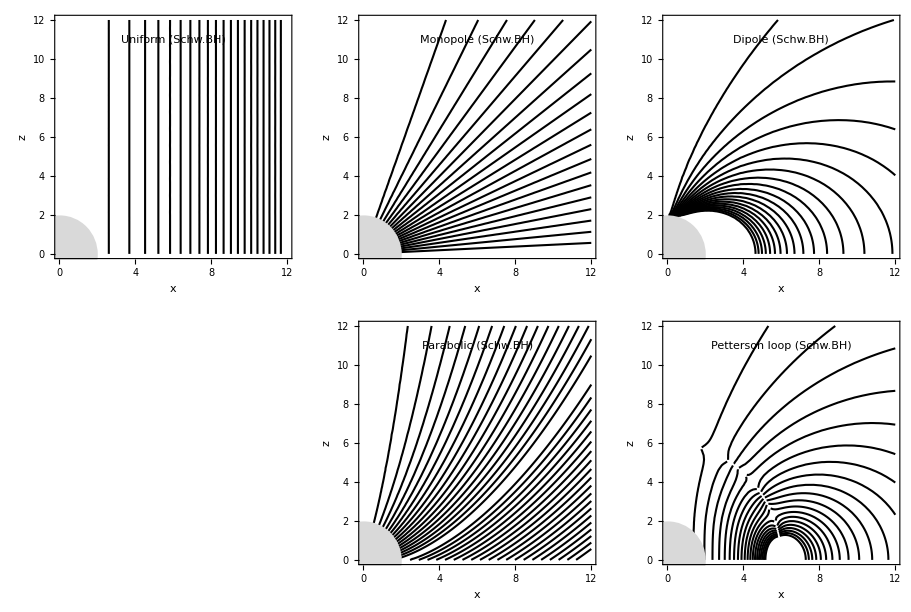

```mathematica
picBH=GraphicsGrid[{{p1,p2,p3},{Null,p5,p4}},Spacings->0]
```

```mathematica
Export["picBH.jpg",picBH];
```